```mathematica
neighborsOf[{i_,j_}]:=Select[Join@@Table[{i+di,j+dj},{di,-1,1},{dj,-1,1}],(*((!#=={i,j} )&&
(And@@((1≤#≤gridwidth)&/@#)))&*)
(((Abs[Plus@@(#-{i,j})]<=1)&&((Times@@(#-{i,j}))==0)))&
]
```

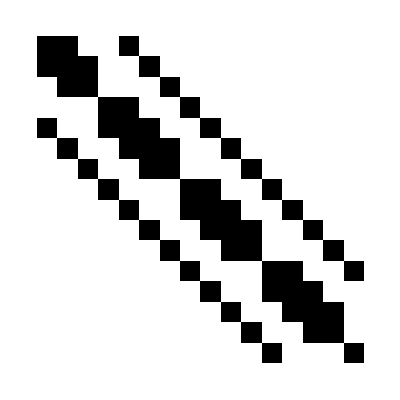

```mathematica
gridwidth = 3;
Clear[neighborMatrix];
	neighborMatrix[gridwidth_]:=neighborMatrix[gridwidth]=Table[If[MemberQ[
neighborsOf[
{Mod[n,gridwidth]+1,Floor[n/gridwidth]+1}],
{Mod[m,gridwidth]+1,Floor[m/gridwidth]+1}],1,0],
{n,gridwidth^2},{m,gridwidth^2}];


neighborMatrix[4]//ArrayPlot
```

```mathematica
Solve[neighborMatrix[4].{-1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16}=={0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16}][[1]]//{x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16}/.#&//Prepend[#,-1]&
```

```mathematica
{-1,1,0,1,0,0,-1,-1,0,0,1,0,1,-1,0,0}
```

{-1,1,0,1,0,0,-1,-1,0,0,1,0,1,-1,0,0}

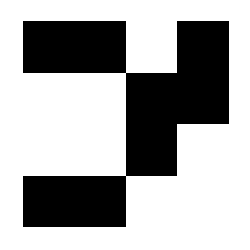

```mathematica
{{-1,1,0,1},{0,0,-1,-1},{0,0,1,0},{1,-1,0,0}}//ArrayPlot
```